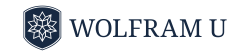

# Introduction to Quantum Computing

## Lesson 4: Bra-Ket Notation

## Overview

Dirac notation is a compact and elegant way to represent quantum states, operators, and the algebraic relations and transformations acting on them. It is a standard language across many areas of quantum theory, especially in quantum information and quantum computing.

## Bra-Ket Notation

Another common notation in quantum is the bra–ket notation. It is also called the Dirac, after the famous British physicist, Paul M. Dirac.

-Graphics-

The Dirac notation offers a compact, clear way to write states, operators, and measurements. In general ket, …, is a shorthand representation for a vector, and bra, …, is the conjugate transpose of a ket. For a qubit, we have:

```mathematica
Row[{ψ->MatrixForm[{α,β}],"  ",ψ->MatrixForm[{{SuperStar[α],SuperStar[β]}}]}]
```

ψ→(α
β)  ψ→(α^* | β^*)

Dirac notation of {1,0}:

```mathematica
QuantumState[{1,0}]//TraditionalForm
```

0

Dirac notation of {0,1}:

```mathematica
QuantumState[{0,1}]//TraditionalForm
```

1

Dirac notation of {α,β}:

```mathematica
QuantumState[{α,β}]//TraditionalForm
```

α0+β1

## Qubit Operators

From these definitions, a ket-bra as …… represents a matrix:

```mathematica
ClearAll[a,b,α,β]
Row[{"ψ"->MatrixForm[{a,b}],"  ","ϕ"->MatrixForm[{α,β}]," => ","ψϕ"->MatrixForm[KroneckerProduct[{a,b},{SuperStar[α],SuperStar[β]}]]}]
```

ψ→(a
b)  ϕ→(α
β) => ψϕ→(a α^* | a β^*
b α^* | b β^*)

Show the matrix form and also Dirac notation of NOT gate:

```mathematica
QuantumOperator["NOT"]
```

01+10

```mathematica
MatrixForm[QuantumOperator["NOT"]["Matrix"]]->TraditionalForm[QuantumOperator["NOT"]]
```

(0 | 1
1 | 0)→01+10

Show the elements in the Dirac notation of R_Y rotation with the angle π/3:

```mathematica
QuantumOperator["RY"[π/3]]
```

(√3)/2 00-1/201+1/2 10+(√3)/2 11

```mathematica
QuantumOperator["RY"[π/3]]["Table"]
```

| 0 | 1
0 | (√3)/2 | -1/2
1 | 1/2 | (√3)/2

## General Operators

Show the Dirac notation of controlled-Hadamard gate:

```mathematica
QuantumOperator["CH"]//TraditionalForm
```

0000+0101+1/(√2)1010+1/(√2)1011+1/(√2)1110-1/(√2)1111

Show the elements in the Dirac notation of CH:

```mathematica
QuantumOperator["CH"]["Table"]
```

| 00 | 01 | 10 | 11
00 | 1 | 0 | 0 | 0
01 | 0 | 1 | 0 | 0
10 | 0 | 0 | 1/(√2) | 1/(√2)
11 | 0 | 0 | 1/(√2) | -1/(√2)

Show the matrix of controlled-Hadamard gate in the computational basis:

```mathematica
QuantumOperator["CH"]["Matrix"]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1/(√2) | 1/(√2)
0 | 0 | 1/(√2) | -1/(√2))

## Summary

Ket notation … represents a complex-valued vector.

Bra notation … can be understood as the conjugate transpose of a ket.

Bra-ket notation …… represents a matrix.

When we have a composite state such as 00, it is shorthand for the tensor product 0⊗0. We will discuss these details further in future chapters